```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
Subscript[ψ, F][x_,y_] = 1/Sqrt[2] * (Subscript[ϕ, 0][x]Subscript[ϕ, 1][y] - Subscript[ϕ, 0][y]Subscript[ϕ, 1][x] );
Subscript[ρ, F][x_,y_] = Integrate[Subscript[ψ, F][x,Subscript[x, 2]]*Subscript[ψ, F][y,Subscript[x, 2]], {Subscript[x, 2],-∞, ∞}];
Subscript[ρ, A][x_,y_,κ_]=Subscript[ρ, F][x,y]-Sign[y-x]*(E^(-Sign[y-x]*I*π*κ)+1)*Integrate[Subscript[ψ, F][x,Subscript[x, 2]]*Subscript[ψ, F][y,Subscript[x, 2]], {Subscript[x, 2],x, y}];
Subscript[n, A][p_,κ_] := 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, A][x,y,κ],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->12,PrecisionGoal->12];
```

```mathematica
Subscript[n, F][p_] = Abs[1/Sqrt[2*π] *  Integrate[E^(-I*p*x)Subscript[ϕ, 0][x],{x,-Infinity,Infinity}] ]^2+Abs[1/Sqrt[2*π]*Integrate[E^(-I*p*x)Subscript[ϕ, 1][x],{x,-Infinity,Infinity}] ]^2;
```

```mathematica
(* Evaluate n(p) at various points to extract momentum tail coefficient *)
domain =  Union[Range[-27,-22,1],Range[22,27,1]];
Subscript[data, κ_]:=Subscript[n, A][domain, κ];
Subscript[CList, κ_]:=domain^4 * Subscript[data, κ];
```

```mathematica
(* I have performed the numerical calculation and then copied the result here so that it would be included in the file when I save it  *)
Subscript[data, 0]={9.630651050669398*^-7,1.120666762590931*^-6,1.3119006454258096*^-6,1.5457687233442804*^-6,1.834217181054339*^-6,2.1932916951125993*^-6,2.1932916951125993*^-6,1.834217181054339*^-6,1.5457687233442804*^-6,1.3119006454258096*^-6,1.120666762590931*^-6,9.630651050669398*^-7};
Subscript[data, 1/5]={8.711008984756918*^-7,1.013652927420146*^-6,1.1866257214366298*^-6,1.3981614225346439*^-6,1.6590654882126282*^-6,1.9838515824519824*^-6,1.983851579140906*^-6,1.6590655079469761*^-6,1.3981613859679628*^-6,1.186625714492298*^-6,1.0136529335592446*^-6,8.711009003974667*^-7};
Subscript[data, 2/5]={6.303345359254883*^-7,7.33486144366722*^-7,8.586504087705515*^-7,1.0117190858602639*^-6,1.2005110622550614*^-6,1.4355284918096212*^-6,1.4355284877346043*^-6,1.2005110677897994*^-6,1.0117190850404152*^-6,8.586504309853593*^-7,7.334861543030911*^-7,6.303345390359334*^-7};
Subscript[data, 3/5]={3.327309458544961*^-7,3.871809578215333*^-7,4.532506923468143*^-7,5.340501327282344*^-7,6.337066216951522*^-7,7.577638843059634*^-7,7.577638643156457*^-7,6.337066272285443*^-7,5.340501319101803*^-7,4.5325068722779846*^-7,3.871809677609565*^-7,3.327309489630431*^-7};
Subscript[data, 4/5]={9.196504745984801*^-8,1.0701449789557174*^-7,1.2527589659522605*^-7,1.4760815297624592*^-7,1.7515290106251282*^-7,2.0944097516204483*^-7,2.0944086165417053*^-7,1.7515277715454224*^-7,1.476075684807494*^-7,1.2527591348940348*^-7,1.070142148097605*^-7,9.196509225326372*^-8};
(* For the sake of time I will not numerically calculate Subscript[data, 1] because we already know the analytic expression for the fermion case *)
Subscript[data, 5/5]=Subscript[n, F][domain];
```

```mathematica
Do[Subscript[data, i/5]=Re[Subscript[data, i/5]],{i,0,5}]
Coeffs={};
Do[Coeffs=Append[Coeffs,Mean[Subscript[CList, i/5]]],{i,0,5}];
Coeffs=Coeffs/Coeffs[[1]](* Divide by the momentum tail coefficient for hardcore bosons because we wish to plot the numerical ratio *)
```

General::munfl: Exp[-729.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.88922×10^-308 0.56419 is too small to represent as a normalized machine number; precision may be lost.

{1.,0.904509,0.654509,0.345492,0.0954918,2.63559×10^-203}

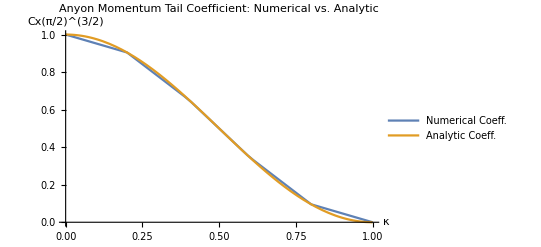

C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/AnyonCoeff.png

C:/Users/Tim/Documents/PhysicsResearch/Poster/AnyonCoeff.png

```mathematica
NumC=Interpolation[Thread[{{0,1/5,2/5,3/5,4/5,1},Coeffs}],InterpolationOrder->1];
AnalyticC[κ_]=Cos[κ*π/2]^2;
p1=Plot[{NumC[x],AnalyticC[x]},{x,0,1},PlotLabel->"Anyon Momentum Tail Coefficient: Numerical vs. Analytic",PlotLegends->{"Numerical Coeff.","Analytic Coeff."},AxesLabel->{"κ","Cx(π/2)^(3/2)"},ImageSize->Scaled[0.5]]
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/AnyonCoeff.png",p1]
Export["C:/Users/Tim/Documents/PhysicsResearch/Poster/AnyonCoeff.png",p1]
```

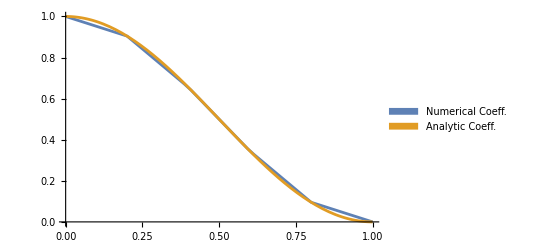

C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Poster/AnyonCoeff.png

```mathematica
p2=Plot[{NumC[x],AnalyticC[x]},{x,0,1},PlotLegends->SwatchLegend[{"Numerical Coeff.","Analytic Coeff."},LabelStyle->{FontWeight->Bold,FontFamily-> "Helvetica",FontSize-> 26}],PlotStyle->{Thickness[.005],Thickness[.005]},ImageSize->Scaled[0.6],BaseStyle->{FontWeight->Bold,FontFamily-> "Helvetica",FontSize-> 26}, AxesStyle->Thick]
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Poster/AnyonCoeff.png",p2]
```